## First Order Shelf, gain > 0 dB

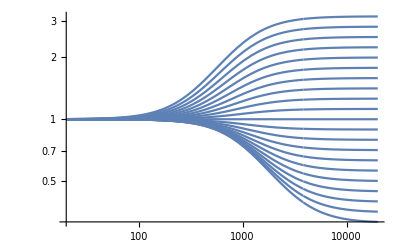

```mathematica
topSide[z_,g_,fc_,fs_]:=Module[{γ,D,b0, b1, a0,a1},
γ = Tan[π fc / fs];
D = γ+1;
b0 = γ+g;
b1 = γ-g;
a1 = γ-1;
b0 /=D;
b1 /=D;
a1 /=D;

(b0 z + b1 )/(z + a1)
]

z[f_,fs_]:=ⅇ^(-ⅈ 2 π f/fs)

dBToGain[dB_]:=10^(dB/20)

Show[
LogLogPlot[Abs[topSide[z[f,48000],dBToGain[#],1000,48000]],{f,20,20000},PlotRange->All]&/@Range[-10,10],PlotRange->All
]
```

## First Order Shelf, gain < 0 dB

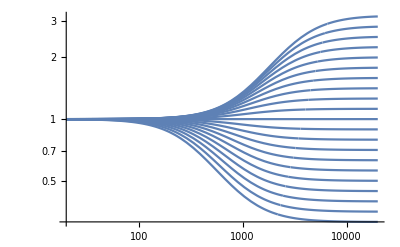

```mathematica
bottomSide[z_,g_,fc_,fs_]:=Module[{γ,D,b0, b1, a0,a1},
γ = Tan[π fc / fs];
D = g γ+1;
b0 = g(γ+1);
b1 = g(γ-1);
a1 = g γ-1;
b0 /=D;
b1 /=D;
a1 /=D;

(b0 z + b1 )/(z + a1)
]

z[f_,fs_]:=ⅇ^(-ⅈ 2 π f/fs)

dBToGain[dB_]:=10^(dB/20)

Show[
LogLogPlot[Abs[bottomSide[z[f,48000],dBToGain[#],1000,48000]],{f,20,20000},PlotRange->All]&/@Range[-10,10],PlotRange->All
]
```

```mathematica
tSide[z_,g_,fc_,fs_]:=Module[{γ,D,b0, b1, a0,a1},
γ = Tan[π fc / fs];
D = γ+1;
b0 = γ+g;
b1 = γ-g;
a1 = γ-1;
b0 /=D;
b1 /=D;
a1 /=D;

{b0,b1,a1}
]

bSide[z_,g_,fc_,fs_]:=Module[{γ,D,b0, b1, a0,a1},
γ = Tan[π fc / fs];
D = g γ+1;
b0 = g(γ+1);
b1 = g(γ-1);
a1 = g γ-1;
b0 /=D;
b1 /=D;
a1 /=D;

{b0,b1,a1}
]
```

## What happens if we do linear interpolation between coefficients for two sets of filters, one with 1.5 dB gain boost and the other with -1.5 dB attenuation? It’s perfect; we get an allpass filter half way through the interpolation. If we just go slowly we should be able to modulate smoothly between + and - gain.

{2.71596,-2.59293,-0.876976}

{0.368194,-0.322898,-0.954703}

{1.,-0.876976,-0.876976}

{1.54208,-1.45792,-0.91584}

1

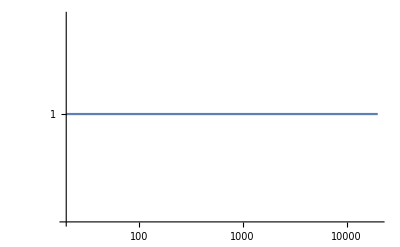

```mathematica
a = tSide[z,2^(1.5),1000,48000]//N
b = bSide[z,2^(-1.5),1000,48000]//N
zero = tSide[z,1,1000,48000]//N
(a + b) / 2
(1 z + -0.8769764629927568 )/(z + -0.8769764629927568)
LogLogPlot[Abs[(1 z[f,48000] + -0.8769764629927568 )/(z[f,48000] + -0.8769764629927568)],{f,20,20000},PlotRange->{0.9,1.1}]
```